## Generating Cos^2 θ Distributions

This section is used to generate the cos^2 θ muon distributions which are used in the cosmic muon simulations. It outputs the distribution to where geant4 is currently configured to read it from.

Setup : 32 scintillators along the x axis and 16 along the y axis
Particles come in X -> Y, Y -> Z, Z -> X
=> 32 scintillators along y axis, 16 along z, x is front

Loss of energy as a function of distance travelled :

```mathematica
pathOutput=NotebookDirectory[]<>"../";
```

```mathematica
6(*GeV*)-0.002(*GeV loss of muons through matter*)*(10000*100(*atmosphere length*)*(1*1000/100^3)(*density of air*)+3*100(*atmosphere length*)*(1.000)(*density of rock*))
```

3.4

```mathematica
nAttempts=100000;
datCos2X=Select[Parallelize[Table[
hx= π(Random[]-1/2);
u=Random[];
If[π/π u<(2 Cos[hx]^2)/π,hx,NA]
,{i,1,nAttempts}]],#>-2&];
ranPhi2X=Table[2π Random[],{i,1,Length[datCos2X]}];
q=-1;m=105.658/1000;
xLength=0./1000.(*m*);yLength=32*2.*1/300(*m*);zLength=16*2.*1/300(*16*);
energy=Table[2.6*Random[]+3.4,{i,1,Length[datCos2X]}];
pNorm=Table[√(energy⟦i⟧^2-m^2),{i,1,Length[datCos2X]}];
(*Format: q m x y z px py pz*)
yzt={y,z,t}/.Table[
Solve[{3.02/1000.,0,0}+{Cos[datCos2X⟦i⟧],Cos[ranPhi2X⟦i⟧]Sin[datCos2X⟦i⟧],Sin[ranPhi2X⟦i⟧]Sin[datCos2X⟦i⟧]}*t=={0,y,z},{y,z,t}]⟦1⟧
,{i,1,Length[datCos2X]}];
XCos2Data=Table[{q,m,xLength,yLength(Random[]-1/2)+yzt⟦i,1⟧,zLength(Random[]-1/2)+yzt⟦i,2⟧,pNorm⟦i⟧ Cos[datCos2X⟦i⟧],pNorm⟦i⟧ Cos[ranPhi2X⟦i⟧]Sin[datCos2X⟦i⟧],
pNorm⟦i⟧ Sin[ranPhi2X⟦i⟧]Sin[datCos2X⟦i⟧]},{i,1,Length[datCos2X]}];
XCos2Data=Select[XCos2Data,Abs[#⟦4⟧]<25&&Abs[#⟦5⟧]<25&];
Length[XCos2Data]
```

31731

```mathematica
Export[pathOutput<>"XCos2Data.dat",XCos2Data];
```

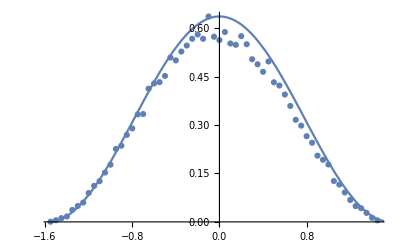

```mathematica
(*We check to make sure the monte carlo above has indeed generated the correct Cos^2 distribution*)
bin=0.05;
HistoListCos2=HistogramList[datCos2X,{bin}];
MaxCountBin=HistoListCos2⟦2⟧//Max;
normFactor=x/.Solve[MaxCountBin*x==2/π,x]⟦1⟧;
listPlotdat3=Table[{HistoListCos2[[1,i]],HistoListCos2[[2,i]]*normFactor},{i,1,Length[HistoListCos2[[2]]]}];
Show[{ListPlot[listPlotdat3],Plot[ 2/π Cos[x]^2,{x,-π/2,π/2}]}]
```

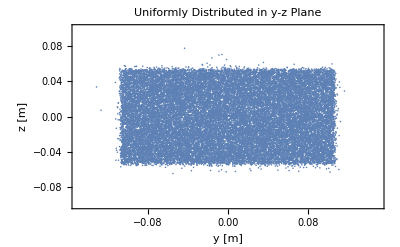

```mathematica
(*This is a plot of the incident hits that will be simulated on the detector*)
(*The detector itself is centered at {y,z}={0,0} and has total length {0.064m,0.032m} so the full detector geometry should be sampled*)
ListPlot[Table[{XCos2Data⟦i,4⟧,XCos2Data⟦i,5⟧},{i,1,Length[XCos2Data]}],PlotLabel->"Uniformly Distributed in y-z Plane",AxesLabel->{"y [m]","z [m]"},Frame->True,PlotRange->{{-0.15,0.15},{-0.1,0.1}}]
```

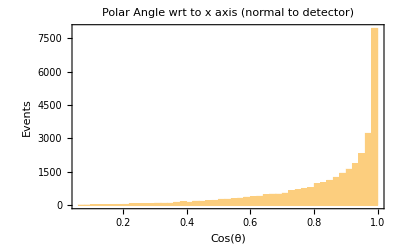

```mathematica
(*We make a histogram of cos(θ)*)
Histogram[Table[XCos2Data⟦i,6⟧/pNorm⟦i⟧,{i,1,Length[XCos2Data]}],50,PlotLabel->"Polar Angle wrt to x axis (normal to detector)",FrameLabel->{"Cos(θ)","Events"},Frame->True]
```

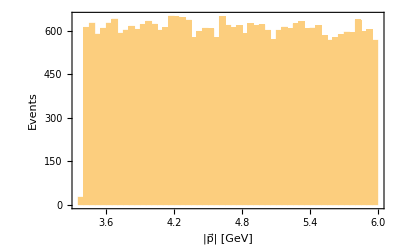

```mathematica
Histogram[pNorm,50,PlotLabel->"",FrameLabel->{"|p⃗| [GeV]","Events"},Frame->True]
```